# Homework week 3 - Paolo Zinesi

## Simulation of Lotka-Volterra equations with different parameters.

```mathematica
a = 10;
c=5;
p=1;
x0 = 1;
y0 = 6;
```

Notation : 	x = Preys, 		y = Predators

```mathematica
sol = NDSolve[{x'[t]==a*x[t]-p*x[t]*y[t], y'[t]==-c*y[t]+p*x[t]*y[t], x[0]==1, y[0]==6},{x,y}, {t,0,100}];
{xt,yt} = Flatten[{x,y}/.sol];
```

```mathematica
sol2 = NDSolve[{x'[t]==a*x[t]-p*x[t]*y[t], y'[t]==-c*y[t]+p*x[t]*y[t], x[0]==6, y[0]==6},{x,y}, {t,0,100}];
{xt2,yt2} = Flatten[{x,y}/.sol2];
```

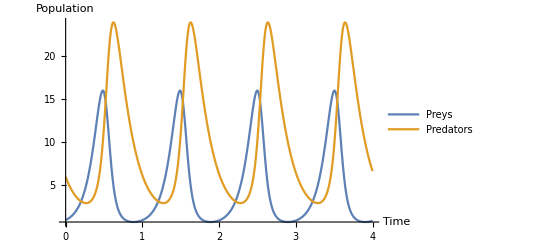

```mathematica
Plot[{xt[t],yt[t]},{t,0,4}, PlotRange->Full, PlotLegends->{"Preys","Predators"}, AxesLabel->{"Time","Population"}]
```

```mathematica
Export["/Users/paolozinesi/Downloads/plot1.jpg",Plot[{xt[t],yt[t]},{t,0,4}, PlotRange->Full, PlotLegends->{"Preys","Predators"}, AxesLabel->{"Time","Population"}]]
```

/Users/paolozinesi/Downloads/plot1.jpg

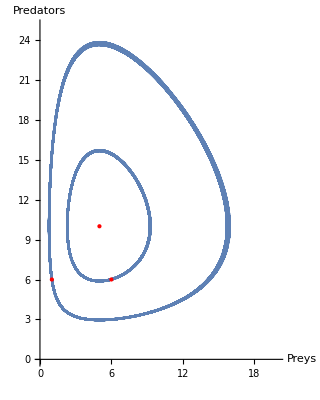

```mathematica
ParametricPlot[{{xt[t],yt[t]},{xt2[t],yt2[t]}}, {t,0,100}, PlotRange->{{0,20},{0,25}},Epilog->{PointSize[Large], Red, Point[{{c/p,a/p},{1,6},{6,6}}]}, AxesLabel->{"Preys","Predators"}, PlotStyle->RGBColor[0.368417, 0.506779, 0.709798]]
```

```mathematica
Export["/Users/paolozinesi/Downloads/paramplot1.png",ParametricPlot[{{xt[t],yt[t]},{xt2[t],yt2[t]}}, {t,0,100}, PlotRange->{{0,20},{0,25}},Epilog->{PointSize[Large], Red, Point[{{c/p,a/p},{1,6},{6,6}}]}, AxesLabel->{"Preys","Predators"}, PlotStyle->RGBColor[0.368417, 0.506779, 0.709798]]]
```

/Users/paolozinesi/Downloads/paramplot1.png

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}